# Kirkpatrick-Seidel’s Prune-and-Search Convex Hull Algorithm

## Выгружаем координаты из файла + запускаем главную функцию

```mathematica
SetDirectory["/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/ConvexHull/Helpers/Text files"];
InputPoints=ReadList["coordinates.txt",Real];
numberOfPoints = IntegerPart [InputPoints[[1]]];
InputPoints = Delete[InputPoints,1];
InputPoints=Partition[InputPoints,2];
```

Для удобства введем EPS для корректного сравнения чисел типа Real:

```mathematica
ϵ = 10^-10;
```

```mathematica
ConvexHull
```

{{-9554.09,-1481.52},{-7011.91,7621.98},{-6327.39,8246.97},{6867.73,9304.36},{8907.37,8420.4},{9825.5,7533.56},{-9554.09,-1481.52},{-8415.11,-4153.95},{-4103.13,-8856.48},{4885.15,-9610.95},{9346.93,-5194.16},{9825.5,7533.56}}

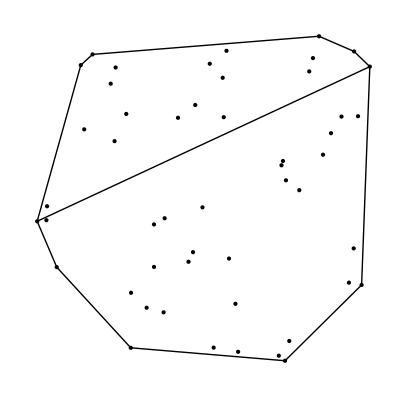

```mathematica
KirkpatrickSeidelConvexHull[InputPoints]
```

## Сперва необходимо найти точки, с которых алгоритм будет начат, то есть точки с максимальным и минимальным X. В том случае, если несколько точек с min/max X лежат на одной вертикали, то для верхней части оболочки пойдет точка с max Y, а для нижней - с min Y; Пример ниже:

## Далее необходимо два раза вызвать функцию построения оболочки - для верхней и нижней соответственно

```mathematica
ConvexHull = {};
```

```mathematica
KirkpatrickSeidelConvexHull[Points_List] :=
 Module[
{
MinX,
MaxX,
MaxUpperPoint,
MinUpperPoint,
MaxLowerPoint,
MinLowerPoint
},
ConvexHull = {};
MinX = Min@Cases[Points, {x_, _} :> x];
MaxX = Max@Cases[Points, {x_, _} :> x];
MinUpperPoint = {
MinX,
Max@Cases[Points, {MinX, y_} :> y]
};
MaxUpperPoint= {
MaxX,
Max@Cases[Points, {MaxX, y_} :> y]
};
 GetPartOfHull[{True, MinUpperPoint, MaxUpperPoint, Points}];
MinLowerPoint = {
MinX,
Min@Cases[Points, {MinX, y_} :> y]
};
MaxLowerPoint= {
MaxX,
Min@Cases[Points, {MaxX, y_} :> y]
};
  GetPartOfHull[{False, MinLowerPoint, MaxLowerPoint, Points}];
Graphics[{Point@Points, Line@ConvexHull}]
]
```

```mathematica
GetPartOfHull[
{
IsUpperHull_,
MinPoint_List, 
MaxPoint_List,
Points_List
}
]:=Module[{Candidates},
If[Norm[MinPoint-MaxPoint]≤ϵ,Return@ MinPoint];
ConnectHull[{IsUpperHull, MinPoint, MaxPoint, Points}];
];
```

## Рекурсивная функция Connect, помогает искать точки оболочки, каждый раз находя такой “bridge”, что все остальные точки лежат ниже или выше этого моста: Connect(firstPoint, secondPoint, SetOfPoints) 1) Ищем медиану точек по координате X; 2) Ищем мост (“самый высокий”) относительной вертикальной линии - медианы X координат. Результатом должна быть пара точек (p, q) образующая линию, которая пересекает хотя бы одну из точек в SetOfPoints слева и справа от медианы, причем так, что ни одна другая точка не лежит выше этой прямой для верхней оболочки; ниже этой прямой - для нижней оболочки. Затем разбиваем SetOfPoints на множество точек, лежащих слева и справа от левой и правой точек моста (p, q) соответственно; -Graphics- 3) Если левая точка моста p == firstPoint => она является точкой оболочки => записываем ее в массив точек выпуклой оболочки; аналогично для правой точки моста q и secondPoint. Если же имеем неравенство, то функция вызывает саму себя для дальнейшего поиска. p != firstPoint => Для левого множества точек: Connect(firstPoint, p, SetOfLeftPoints); q != secondPoint => Для правого множества точек: Connect(q, secondPoint, SetOfRightPoints); И уже в них производится попытка найти точки выпуклой оболочки;

```mathematica
ConnectHull[
{
IsUpperHull_,
FirstPoint_List,
SecondPoint_List,
Points_List
}
]:=Module[
{
MedianX,
Bridge={},
LeftPoints={},
RightPoints={}
},
MedianX=Median@Cases[Points,{x_Real,y_Real}:>x];
Bridge = Sort[MakeBridge[{Points, MedianX, IsUpperHull}], #1[[1]] < #2[[1]] & ];
LeftPoints = Partition[Flatten@Join[
Bridge[[1]],
Cases[ Points, {x_, _} /; (x < Bridge[[1, 1]]) ]
],2];
RightPoints = Partition[Flatten@Join[
Bridge[[2]],
Cases[ Points, {x_, _} /; (x > Bridge[[2, 1]]) ]
],2];

If[ Bridge[[1]] == FirstPoint,
AppendTo[ConvexHull,FirstPoint],
ConnectHull[{IsUpperHull, FirstPoint, Bridge[[1]], LeftPoints}];
];

If[ Bridge[[2]] == SecondPoint, 
AppendTo[ConvexHull,SecondPoint],
ConnectHull[{IsUpperHull, Bridge[[2]], SecondPoint, RightPoints}];
];
];
```

## Построение моста (“Bridge”)

## Основная и самая сложная часть алгоритма - поиск моста (“Bridge”). На вход принимает список точек, относительно которых ищется мост; медиану их X’ых координат. Переменная isUpperBridge - флаг, определяющий для какой именно части оболочки мы строим мост (поэтому необходимо ввести 2 вспомогательные функции - continueFor[Upper/Lower]Bridge) Ниже будет показана картинка, иллюстрирующая ход алгоритма: 1) Если на вход получили всего 2 точки, то возвращаем их и выходим из функции; 2) Разбиваем точки на пары точек, причем x1 <= x2. Если на вход получено нечетное количество точек, то первую из них записываем в список точек-кандидатов (для дальнейших итераций рекурсивной функции Bridge), а остальные разбиваем на пары точек; 3)

```mathematica
Slope[{{x1_,y1_},{x2_,y2_}}]:=(y1-y2)/(x1-x2);


ContinueForUpperBridge[
{
MedianX_,
MedianSlope_,
SmallPairs_List,
LargePairs_List,
EqualPairs_List,
Points_List,
CandidatesInput_List
}
]:=Module[
{
Candidates = CandidatesInput,
Height,
PointsOnTheMaximizedLine = {},
LargeAndEqualPairs = {},
SmallAndEqualPairs = {},
MaximizedMinPoint,
MaximizedMaxPoint
},
Height  = Max@Cases[Points, {x_, y_} :> (y - MedianSlope *x) ];
PointsOnTheMaximizedLine = Sort[
Cases[Points, {x_, y_} /; (Abs[(y - MedianSlope *x) - Height] ≤ϵ)],
#1[[1]]<#2[[1]]&
];
MaximizedMinPoint = First[PointsOnTheMaximizedLine];
MaximizedMaxPoint = Last[PointsOnTheMaximizedLine];
If[MaximizedMinPoint[[1]] ≤ MedianX && MaximizedMaxPoint[[1]] > MedianX,
Return[{{MaximizedMinPoint, MaximizedMaxPoint}}]
];

If[ MaximizedMaxPoint[[1]] ≤ MedianX,
LargeAndEqualPairs = Join[LargePairs, EqualPairs];
Candidates = Partition[Flatten@Join[
Candidates, 
Join[#[[2]] &/@ LargeAndEqualPairs, Flatten[SmallPairs, 1]]
]
, 2
];
];

If[ MaximizedMinPoint[[1]] > MedianX,
SmallAndEqualPairs = Join[SmallPairs, EqualPairs];
Candidates = Partition[Flatten@Join[
Candidates, 
Join[#[[1]] &/@ SmallAndEqualPairs, Flatten[LargePairs, 1]]
]
, 2
];
];
Return[Candidates]
];
```

```mathematica
ContinueForLowerBridge[
{
MedianX_,
MedianSlope_,
SmallPairs_List,
LargePairs_List,
EqualPairs_List,
Points_List,
CandidatesInput_List
}
]:=Module[
{
Candidates = CandidatesInput,
Height,
PointsOnTheMinimizedLine = {},
LargeAndEqualPairs = {},
SmallAndEqualPairs = {},
MinimizedMinPoint,
MinimizedMaxPoint
},
Height  = Min@Cases[Points, {x_, y_} :> (y - MedianSlope *x) ];
PointsOnTheMinimizedLine = Sort[
Cases[Points, {x_, y_} /; (Abs[(y - MedianSlope *x) - Height] ≤ϵ)],
#1[[1]]<#2[[1]]&
];
MinimizedMinPoint = First[PointsOnTheMinimizedLine];
MinimizedMaxPoint = Last[PointsOnTheMinimizedLine];
If[MinimizedMinPoint[[1]] ≤ MedianX && MinimizedMaxPoint[[1]] > MedianX,
Return[{{MinimizedMinPoint, MinimizedMaxPoint}}]
];

If[ MinimizedMaxPoint[[1]] ≤ MedianX,
SmallAndEqualPairs = Join[SmallPairs, EqualPairs];
Candidates = Partition[Flatten@Join[
Candidates, 
Join[#[[2]] &/@ SmallAndEqualPairs, Flatten[LargePairs, 1]]
]
, 2
];
];

If[ MinimizedMinPoint[[1]] > MedianX,
LargeAndEqualPairs =Join[LargePairs, EqualPairs];
Candidates = Partition[Flatten@Join[
Candidates, 
Join[#[[1]] &/@ LargeAndEqualPairs, Flatten[SmallPairs, 1]]
]
, 2
];
];

Return[Candidates]
];
```

```mathematica
MakeBridge[
{
Points_List,
MedianX_,
IsUpperBridge_
}
]:=Module[
{
RemainingPoints = Points,
Candidates={},
PointPairs = {},
Slopes = {},
MedianSlope,
EqualXCasesPoints = {},
SmallPairs={},
LargePairs={},
EqualPairs={},
BridgeOrCandidates = {},
Temp
},

If[Length@RemainingPoints==2,
Return[RemainingPoints]
];

Temp = RemainingPoints;
If[OddQ@Length@RemainingPoints,
AppendTo[Candidates,RemainingPoints[[1]]];
Temp=Delete[RemainingPoints,{1}];
];
PointPairs=Partition[Sort[Temp, #1[[1]]<#2[[1]]&],2];
EqualXCasesPoints=Cases[PointPairs, {{x1_,y1_},{x2_,y2_}}/;(Abs[x1-x2]<=ϵ)];
Candidates = Partition[Flatten@AppendTo[Candidates,Cases[EqualXCasesPoints,{{x1_,y1_},{x2_,y2_}}:>If[y2>y1,{x2,y2},{x1,y1}]]
],
2
];
PointPairs=Complement[PointPairs,EqualXCasesPoints];
Slopes=(Slope[#])&/@ (PointPairs);
MedianSlope=Median@Slopes;
(If[Abs[Slope[#]-MedianSlope] ≤ ϵ ,
AppendTo[EqualPairs,#],
If[Slope[#]<MedianSlope,
AppendTo[SmallPairs,#],
AppendTo[LargePairs,#]]
])&/@PointPairs;
BridgeOrCandidates=
If[IsUpperBridge,
 ContinueForUpperBridge[{MedianX, MedianSlope, SmallPairs, LargePairs, EqualPairs, RemainingPoints, Candidates}],
ContinueForLowerBridge[{MedianX, MedianSlope, SmallPairs, LargePairs, EqualPairs, RemainingPoints, Candidates}]
];
If[Length@BridgeOrCandidates == 1,
Return[ BridgeOrCandidates[[1]]],
Return[MakeBridge[{Sort[BridgeOrCandidates, #1[[1]]<#2[[1]]&], MedianX, IsUpperBridge}]]
];
];
```

```mathematica
a = {{1241, 543}, {123, 54}, {124, 323}};
```

```mathematica
a = Reverse@a
```

{{124,323},{123,54},{1241,543}}

```mathematica
a
```

{{124,323},{123,54},{1241,543}}